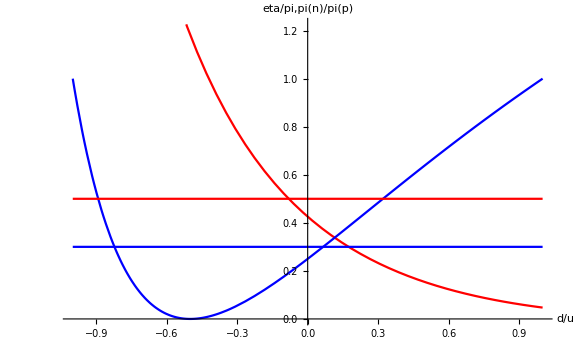

0.425633

0.25

```mathematica
etapi[x_]:= (1.13/Sqrt[3](2-x)/(2+x))^2;
np[x_]:=((1+2x)/(2+x))^2;

Plot[{etapi[x],np[x],0.5,0.3},{x,-1,1},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"d/u","eta/pi,pi(n)/pi(p)"}]
etapi[0.]
np[0.]
```